```mathematica
Clear["Global`*"]
```

g2 plot from theory paper (plot repeated in matlab)

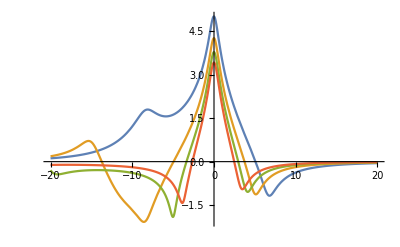

```mathematica
k = 1;
gamma=k;
eps = 0.01;

dap = da - I*k/2;
dop = do -I*gamma/2;
C2g = (eps^2* ((dap + dop)*dop + g^2))/(Sqrt[2](dap*dop-g^2)*((dap+dop)*dap-g^2));
C1g = (eps*dop)/(g^2-dap*dop);
g2 = (2*Abs[C2g]^2)/Abs[C1g]^4;
lg2 = Log10[g2];
strongc = lg2 /.g->10;
Plot[{strongc /.da->15,strongc /.da->20,strongc /.da->25,strongc /.da->30}, {do,-20,20},PlotRange->All]
```

Section A
Energy eigenvalues for strong coupling

```mathematica
H = {{n*wa,g*Sqrt[n]},{g*Sqrt[n],wo+(n-1)*wa}};
MatrixForm[H]
Eigenvalues[H]
```

(n wa | g √n
g √n | (-1+n) wa+wo)

{1/2 (-wa+2 n wa+wo-√(4 g^2 n+wa^2-2 wa wo+wo^2)),1/2 (-wa+2 n wa+wo+√(4 g^2 n+wa^2-2 wa wo+wo^2))}

Section B
Coefficients for g2

```mathematica
Psi = {c0g[t], c1g[t],c0e[t],c2g[t],c1e[t]}; MatrixForm[Psi]
```

(c0g[t]
c1g[t]
c0e[t]
c2g[t]
c1e[t])

```mathematica
lhs = D[Psi, t];

eqlist1= Thread[rhs == lhs]; MatrixForm[eqlist1] /. notation
```